In this notebook is simulated a One self-Regulated gene with GA and the three-stage model (burst expression). The notebook has two parts:
1. To evaluate the “sensitivity” to the whole set the parameters. With an arbitrary start point to calculate the estimates (FF, CV2,Mean) (30% of the total number of iterations), and different number of iterations to get a final t of 1500. 
3. To evaluate 4 specific regions

## Parameters for the two sessions

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
name=0.5; (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg";(* With the name of the second parameter is named the output file *)
parametro1="kg_";
parametro2="_γg_";
```

These are the default values of parameters

```mathematica
Clear[kg,γg,km,γm,kp,γp,τ];
kg=0.01158;(* Gene activation rate (t^-1)*)
γg=2.082;(* Gene desactivation rate (t^-1) *)
km=0.696;(* Production rate of mRNA (molecules*t^-1) *)
γm=0.02082(*degradation mRNA*);
kp=1.386(*syntesis proteins*);
γp=0.02082(*degradation proteins*);
h=3.0; (* Michaelis-Menten constant *)
kAA=100(* Hill's constant *);
```

## Functions for the two sessions

These are the reactions (changesByRXN) and propensity functions (pF) of the GA for the specific regulation system: self-regulated gene

```mathematica
changesByRXN=Function/@<|1->{#1,#2,#3-1,#4+1},2->{#1,#2,#3+1,#4-1},3->{#1+1,#2,#3,#4},4->{#1-1,#2,#3,#4},5->{#1,#2+1,#3,#4},6->{#1,#2-1,#3,#4}|>;(* Each hash represents a specie: mRNA,protein,da0:InactivatedPromoter,da1:ActivatedPromoter. The numbers are the next reactions: 1-activation, 2-deactivation, 3-5 synthesis, 4-6 degradation *)pF=Compile[{{kg,_Real},{γg,_Real},{km,_Real},{γm,_Real},{kp,_Real},{γp,_Real},{h,_Real},{kAA,_Real},{a,_Integer},{p,_Integer},{da0,_Integer},{da1,_Integer}},{da0*kg*(p ^h/(kAA+p ^h)),da1*γg,da1*km+0.01(*Esto para mantener una expresión basal como en el de Langevin (que no tiene ceros)y que el kon no se haga cero*),a*γm,kp*a,γp*p},RuntimeAttributes->{Listable},Parallelization->True];
```

This is equal for all  sub-circuits

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]];(* Fano Factor for noise measure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* Squared Coefficient of Variation for noise measure *)
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013 *)steadyStateStart[window_,listData_]:=Block[{n,dataByWindow,mPorVentana,μ,sd,probabilidades},
n=Floor[Length[#]/window]&[listData];
dataByWindow=Partition[#,n]&[listData[[All,2]]];mPorVentana=Map[Mean[#[[2;;All]]-#[[1;;-2]]]&,dataByWindow];μ=MapThread[(1/n)(Total[#1]-#2*Total[Range[1,n](*tPorVentana*)])&,{dataByWindow,mPorVentana}];sd=Table[Sqrt[(1/(n-2))*Sum[(dataByWindow[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[dataByWindow[[i]]]}]],{i,window}];probabilidades=Map[Total[#]/n&,Table[If[Abs[dataByWindow[[i,j]]-μ[[i]]]≤sd[[i]],1,0],{i,window},{j,1,n}]]//N;
((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1]
```

```mathematica
plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp]}]
```

## S1: All range parameters values

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=5; (* Number of times the algorithm is run *)
```

### Simulation

```mathematica
(* Launch the number of kernels in which you will parallelize the simulation *)
LaunchKernels[8]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

Here there is a detail that changes by sub-circuit : the number and type of Kmm (put it in the arguments of the function simu, in the DistributeDefinitions, and pF function)

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
DistributeDefinitions[pF,h,kAA,kg,γg,km,γm,kp,γp,changesByRXN,ff,expressionNoise,iteraciones1];
(*List by parameters*)
mRNAffcv2List={};
proteinffcv2List={};

Do[
(*List by replicates*)
listEstimatemRNA={};
     listEstimateprotein={};
 listDataAndTimeT={};

SetSharedVariable[listEstimatemRNA,listEstimateprotein,listDataAndTimeT];

ParallelDo[

listDataAndTime = CreateDataStructure["OrderedHashSet"];
abundancia={1,1,1,0}(*mRNA,protein,da0,da1*);
t=0;

Do[
τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[kg,γg,km,γm,kp,γp,h,kAA,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];         
 listDataAndTime["Union", {{t, abundancia}}];
            If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones1 ];

  listData = Normal[listDataAndTime][[All, 2]];
        ini =Echo@Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)
{mRNAffcv2It,proteinffcv2It}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];

AppendTo[listEstimatemRNA,mRNAffcv2It];
AppendTo[listEstimateprotein,proteinffcv2It];
  AppendTo[listDataAndTimeT, listDataAndTime];


,replicas1];

AppendTo[mRNAffcv2List,Mean[listEstimatemRNA]];
AppendTo[proteinffcv2List,Mean[listEstimateprotein]],

    
 {kg,{1}},{γg,{0.01}}]; (*CAMBIAR AQUI EN EL .m*)
```

>> 39519

>> 40360

>> 43775

>> 46458

```mathematica
Export["controlRGA_"<>parametro<>ToString[name]<>".csv",{mRNAffcv2List,proteinffcv2List}];
```

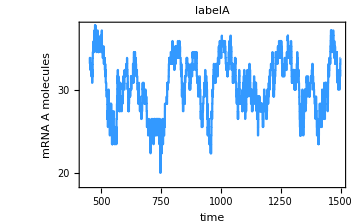
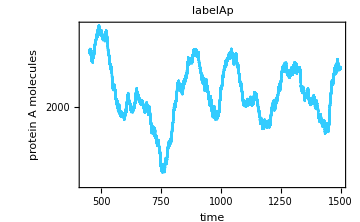
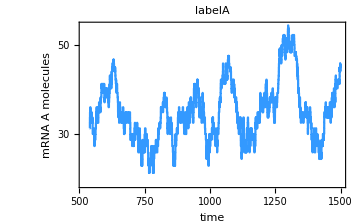
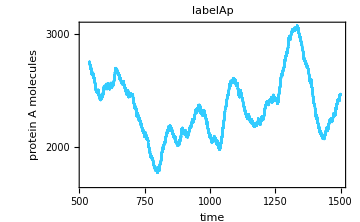
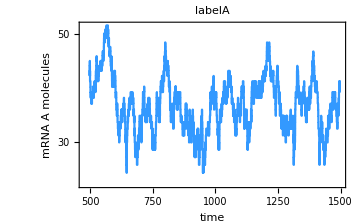
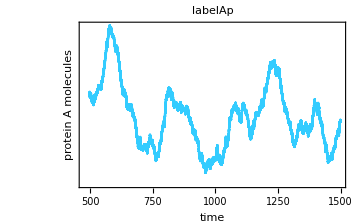
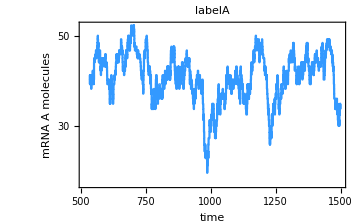
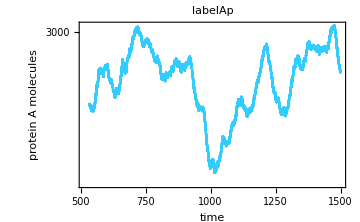

```mathematica
listDataAndTimeTN=Normal/@listDataAndTimeT;
MapThread[plotsLogExpression[#1,#2,listDataAndTimeTN,"","",""]&,{Range[1,replicas1],{39519,40360,43775,46458}}]
```

## S2: Evaluation by regions

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=5; (* Number of times the algorithm is run *)
rep=1; (* Some plots are made with the output of this replicate*)
lagStep=10; (* Lag time for the Autocorrelation plot *)
species=2;(*mRNA genA/B protein genA/B*)
```

### Functions

These functions make different plots of the temporal genes expression

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins *)plotsExpression[rep_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLinePlot,Frame-> True,ImageSize->Medium];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLinePlot[datesListAm,PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLinePlot[datesListAp,PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp]}]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp]}]
```

```mathematica
(* This plots the auto-correlation of the temporal dynamic of genes mRNA and proteins *)autoCorrPlot[lagStep_,listDataAndTimeTN_,positions_]:=Module[{data,lenght,data2,corr,negatives,cortes},
data=Table[MapThread[Extract[#1,#2]&,{listDataAndTimeTN[[All,All,2]][[All,All,i]],positions}],{i,{1,2}}];
lenght=Min[Length/@#]&/@data;
data2=MapThread[TemporalData[#1[[All,1;;#2]],{Range[1,#2]}]&,{data,lenght}](*This is to get the corr in each lag time as the average between replicates *);
DistributeDefinitions[data,data2];
corr=ParallelMap[CorrelationFunction[#,{1,#["PathLengths"][[1]]-1,lagStep}]&,data2];
negatives=FirstPosition[Normal[#],{_,_?Negative}]*lagStep&/@corr;
cortes=Count[Partition[#//Normal,2,1],{{_,_?Positive},{_,_?Negative}}|{{_,_?Negative},{_,_?Positive}}]&/@corr;
ListPlot[#[[1]],Filling->Axis ,Frame->True,ImageSize->Medium,FrameLabel->{"Lag-"<>ToString[lagStep],#[[2]]},PlotStyle->#[[4]],PlotLabel->"First negative: "<>ToString[#[[3]]]<>"\n cortes: "<>ToString[#[[5]]]]&/@{{corr[[1]],"mRNA A",negatives[[1]],RGBColor[0.2,0.6,1],cortes[[1]]},{corr[[2]],"protein A",negatives[[2]],RGBColor[0.2,0.8,1],cortes[[2]]}}]
```

```mathematica
(* This plots the histogram of the steady state gene expression for mRNA and proteins *)distriPlot[ini_,listDataAndTimeTN_]:=Module[{distribucionAm,distribucionAp},
{distribucionAm,distribucionAp}=Table[Flatten[listDataAndTimeTN[[All,All,2]][[All,ini;;All,i]]],{i,2}];Histogram[#[[1]],Automatic(*{Min[#[[1]]]//Round,Max[#[[1]]]//Round,5}*),"Probability",FrameLabel->{#[[2]],"Probability"},PlotLabel->#[[4]]<>" \n FF: "<>ToString[ff[#[[1]]]]<>", CV^2: "<>ToString[expressionNoise[#[[1]]]]<>", Mean: "<>ToString[Mean[#[[1]]]//N],ChartStyle->#[[3]],Frame->True,ImageSize->Medium]&/@{{distribucionAm,"mRNA A molecules",RGBColor[0.2,0.6,1],labelA},{distribucionAp,"protein A molecules",RGBColor[0.2,0.8,1],labelAp}}]
```

```mathematica
(* This plots the velocity of the temporal dynamic of  gene expression *)
veloPlot[rep_,listDataAndTimeTN_,positionsVelocity_]:=Module[{listS,listT,velocidades},
listS=Table[Extract[#[[All,i]],positionsVelocity],{i,2}]&[listDataAndTimeTN[[rep,All,2]]];
listT=Extract[#,positionsVelocity]&[listDataAndTimeTN[[rep,All,1]]];
velocidades=Table[(listS[[i,2;;]]-listS[[i,;;-2]])/(listT[[2;;]]-listT[[;;-2]]),{i,2}];
Table[ListLinePlot[Transpose[{listT[[2;;]],velocidades[[i[[1]]]]}],PlotStyle->i[[2]],PlotLabel->"Velocities",FrameLabel->{"time",i[[3]]}],{i,{{1,RGBColor[0.2,0.6,1],"mRNA A molecules"},{2,RGBColor[0.2,0.8,1],"protein A molecules"}}}]]
```

Here there is a detail that changes by sub-circuit : the number and type of Kmm (put it in the arguments of the function simu, in the DistributeDefinitions, and pF function)

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
simu[iteraciones_,replicas_,h_,kAA_,kgA_,γgA_,kmA_,γmA_,kpA_,γpA_,rep_,parametros_,lagStep_,species_]:=

Module[{ini,listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT,listDataAndTime,t,abundancia,τis,reactionAndτμ,listData,mRNAffcv2ItA,proteinffcv2ItA,mRNAffcv2ItI,proteinffcv2ItI,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,listDataAndTimeTN,positions},

DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,steadyStateStart,iteraciones,h,kAA,kgA,γgA,kmA,γmA,kpA,γpA];

listEstimatemRNAA={};
listEstimateproteinA={};
listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listDataAndTimeT];

ParallelDo[

listDataAndTime=CreateDataStructure["OrderedHashSet"];
t=0;
abundancia={1,1,1,0}(*mRNAA,proteinA,da0A,da1A*);


Do[
          τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[kgA,γgA,kmA,γmA,kpA,γpA,h,kAA,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];listDataAndTime["Union",{{t,abundancia}}];
If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones];

listData=Normal[listDataAndTime][[All,2]];
 ini =Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)

{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listDataAndTimeT,listDataAndTime];,

replicas];

mRNAffcv2MeanA=Mean[listEstimatemRNAA];
proteinffcv2MeanA=Mean[listEstimateproteinA];

Export["controlRGA_"<>parametros<>".csv",{listEstimatemRNAA,listEstimateproteinA}];

listDataAndTimeTN=Normal/@listDataAndTimeT;

{labelA,labelAp}=Table["FF: "<>ToString[i[[1]]]<>" CV2: "<>ToString[i[[2]]]<>" Mean: "<>ToString[i[[3]]]<>parametros,{i,{mRNAffcv2MeanA,proteinffcv2MeanA}}];

 ini =Round[(Length[listDataAndTimeTN[[rep]]]*30)/100.] ;

positions=Table[DeleteCases[FirstPosition[listDataAndTimeTN[[i,All,1]]//Round,#]&/@Range[1,1500,1],Missing["NotFound"]],{i,replicas}];(* These are the positions the ~1500 points to get the velocities and the auto-correlation plot*)

{plotsExpression[rep,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,parametros],
plotsLogExpression[rep,ini,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,parametros],
autoCorrPlot[lagStep,listDataAndTimeTN,positions],
distriPlot[ini,listDataAndTimeTN],
veloPlot[rep,listDataAndTimeTN,positions[[rep]]],listDataAndTimeT}]
```

### Simulation

```mathematica
s=Flatten[Table[simu[iteraciones2,replicas2,h,kAA,kg,γg,km,γm,kp,γp,rep,"\n kgA: " <>ToString[kg]<>" γgA: "<>ToString[γg](*parametros*),lagStep,species],{kg,{0.05}},{γg,{0.2}}],{3}];
```

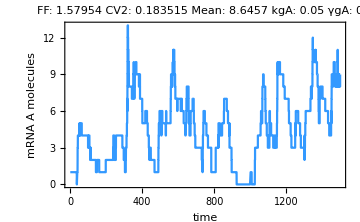
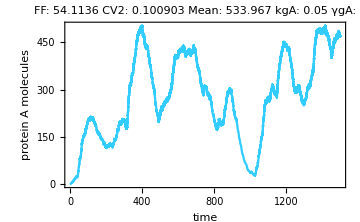
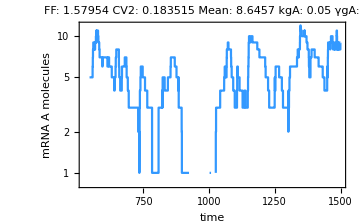
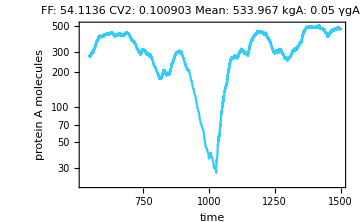
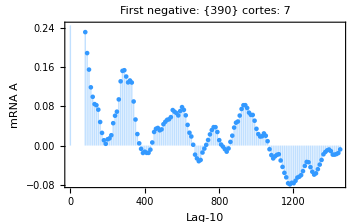
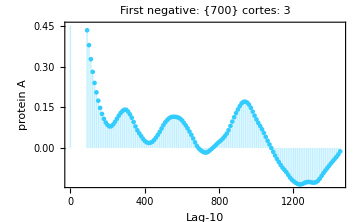
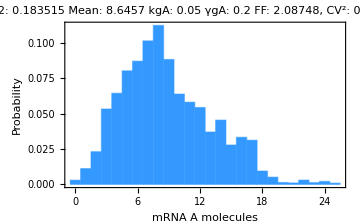
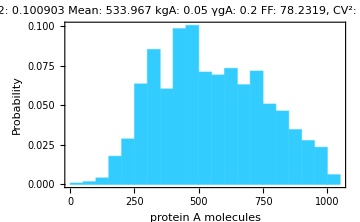
{{{{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-}}},{{{DataStructure[OrderedHashSet, {Data -> {{0.420691, {1, 2, 1, 0}}, {2.33902, {1, 1, 1, 0}}, {2.58789, {1, 2, 1, 0}}, {3.97203, {1, 3, 1, 0}}, {5.83173, {1, 4, 1, 0}}, {7.01335, {1, 5, 1, 0}}, {8.93413, {1, 6, 1, 0}}, {9.43257, {1, 7, 1, 0}}, {11.2971, {<<4>>}}, <<18521>>, {1499.45, {9, 471, 0, 1}}, {1499.45, {9, 472, 0, 1}}, {1499.49, {9, 473, 0, 1}}, {1499.58, {9, 472, 0, 1}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0805103, {1, 2, 1, 0}}, {0.451892, {1, 3, 1, 0}}, {0.601798, {1, 4, 1, 0}}, {0.82567, {1, 5, 1, 0}}, {2.41449, {1, 6, 1, 0}}, {2.52836, {1, 7, 1, 0}}, {3.89909, {1, 8, 1, 0}}, {4.63521, {1, 9, 1, 0}}, {4.66694, <<1>>}, <<26150>>, {1499.28, {3, 293, 1, 0}}, {1499.35, {3, 292, 1, 0}}, {1499.5, {3, 291, 1, 0}}, {1499.51, {3, 290, 1, 0}}}}],DataStructure[OrderedHashSet, {Data -> {{0.0519687, {1, 2, 1, 0}}, {0.109399, {1, 3, 1, 0}}, {0.266688, {1, 4, 1, 0}}, {1.0615, {1, 5, 1, 0}}, {1.73868, {1, 6, 1, 0}}, {1.91308, {1, 7, 1, 0}}, {3.0603, {1, 8, 1, 0}}, {3.433, {1, 9, 1, 0}}, {4.79236, {<<4>>}}, <<29868>>, {1499.45, {9, 722, 0, 1}}, {1499.47, {9, 723, 0, 1}}, {1499.49, {9, 722, 0, 1}}, {1499.54, {10, 722, 0, 1}}}}],DataStructure[OrderedHashSet, {Data -> {{0.723809, {1, 2, 1, 0}}, {0.980403, {1, 3, 1, 0}}, {2.32449, {1, 4, 1, 0}}, {2.99419, {1, 5, 1, 0}}, {4.37278, {1, 6, 1, 0}}, {4.83945, {1, 7, 1, 0}}, {5.18765, {1, 8, 1, 0}}, {5.78428, {1, 9, 1, 0}}, {5.84472, <<1>>}, <<32987>>, {1499.49, {4, 511, 1, 0}}, {1499.49, {4, 510, 1, 0}}, {1499.49, {4, 509, 1, 0}}, {1499.51, {4, 508, 1, 0}}}}]}}}}

```mathematica
s
```